```mathematica
(*  Guy F. Mongelli                               ChE 400
   Prof. Clark                                   9/26/2010     *)
```

```mathematica
(*  Assignment #5 *)
```

```mathematica
(* Problem #1  *)
(* Developing a fourier sine series that approximates the initial condition.  This codfe is taken from the workbook developed for Assignment #4, Problem 1, part B  *)
```

```mathematica
(* Part B *)
```

```mathematica
(* Now consider the Fourier Sine Series for F.  The Fourier Sine Series is the periodic extension of the odd extension of x. *)
```

```mathematica
T0=100 (* deg C *);
a=2;
b=1;
L=a;
fbas[x_]:=4*T0(x/a)(1-x/a);
```

```mathematica
fbasod[x_]:=If[(x≥0),fbas[x],-fbas[-x]];
fod[x_]:=fbasod[Mod[x,2*L,-L]];
```

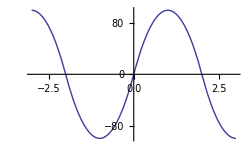

```mathematica
graphoneFSine=Plot[fod[x],{x,-3,3}]
```

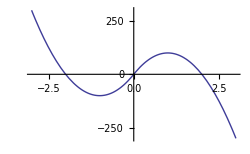

```mathematica
Plot[fbasod[x],{x,-3,3}]
```

```mathematica
(* The odd extended function is discontinuous every 2L period.  Therefore, the periodic extension of the odd extension will have foruier coefficients that drop of as 1/n.  *)
```

```mathematica
aFSine[0]=1/(2L)∫_-L^L fod[x]ⅆx
```

0

```mathematica
aFSine[n_]=Simplify[1/L∫_-L^L fod[x]Cos[(n π x)/L]ⅆx,n∈Integers]
```

0

```mathematica
bFSine[n_]=Simplify[(2*T0)/Cosh[(n π b)/a]∫_0^L fod[x]Sin[(n π x)/L]ⅆx,n∈Integers]
```

-(160000 (-1+(-1)^n) Sech[2 n π])/(n^3 π^3)

```mathematica
coeffsFSine=Table[{aFSine[i],bFSine[i]},{i,1,20}];
TableForm[coeffsFSine]
```

0 | (320000 Sech[2 π])/π^3
0 | 0
0 | (320000 Sech[6 π])/(27 π^3)
0 | 0
0 | (2560 Sech[10 π])/π^3
0 | 0
0 | (320000 Sech[14 π])/(343 π^3)
0 | 0
0 | (320000 Sech[18 π])/(729 π^3)
0 | 0
0 | (320000 Sech[22 π])/(1331 π^3)
0 | 0
0 | (320000 Sech[26 π])/(2197 π^3)
0 | 0
0 | (2560 Sech[30 π])/(27 π^3)
0 | 0
0 | (320000 Sech[34 π])/(4913 π^3)
0 | 0
0 | (320000 Sech[38 π])/(6859 π^3)
0 | 0

```mathematica
FxComp[k_,x_]:=coeffsFSine[[k,2]]*Sin[k*Pi*x/L]+coeffsFSine[[k,1]]*Cos[k*Pi*x/L]
```

```mathematica
FyComp[k_,y_]:=(8*T0)/π^3 1/(2k+1)^3 Cosh[(2k+1)π y/a]/Cosh[(2k+1)π b/a]
```

```mathematica
Fx[N_,x_,y_]=∑_(n=1)^N FxComp[k,x]*FyComp[k,y]
```

Part::pspec: Part specification k is neither an integer nor a list of integers.

General::stop: Further output of Part will be suppressed during this calculation.

1/((1+2 k)^3 π^3)800 N Cosh[(1+2 k) π y] Sech[2 (1+2 k) π] (Cos[k π x] {{0,(320000 Sech[2 π])/π^3},{0,0},{0,(320000 Sech[6 π])/(27 π^3)},{0,0},{0,(2560 Sech[10 π])/π^3},{0,0},{0,(320000 Sech[14 π])/(343 π^3)},{0,0},{0,(320000 Sech[18 π])/(729 π^3)},{0,0},{0,(320000 Sech[22 π])/(1331 π^3)},{0,0},{0,(320000 Sech[26 π])/(2197 π^3)},{0,0},{0,(2560 Sech[30 π])/(27 π^3)},{0,0},{0,(320000 Sech[34 π])/(4913 π^3)},{0,0},{0,(320000 Sech[38 π])/(6859 π^3)},{0,0}}⟦k,1⟧+{{0,(320000 Sech[2 π])/π^3},{0,0},{0,(320000 Sech[6 π])/(27 π^3)},{0,0},{0,(2560 Sech[10 π])/π^3},{0,0},{0,(320000 Sech[14 π])/(343 π^3)},{0,0},{0,(320000 Sech[18 π])/(729 π^3)},{0,0},{0,(320000 Sech[22 π])/(1331 π^3)},{0,0},{0,(320000 Sech[26 π])/(2197 π^3)},{0,0},{0,(2560 Sech[30 π])/(27 π^3)},{0,0},{0,(320000 Sech[34 π])/(4913 π^3)},{0,0},{0,(320000 Sech[38 π])/(6859 π^3)},{0,0}}⟦k,2⟧ Sin[k π x])

```mathematica
fourierFSine[k_,x_,y_]:=∑_(k=1)^k FsSine[k,x]FyComp[k,y]
```

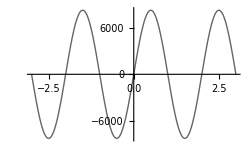

```mathematica
graphtwoFSine=Plot[fourierFSine[5,x],{x,-3,3},PlotStyle->GrayLevel[0.4]]
```

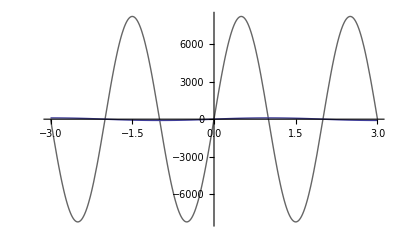

```mathematica
bothtwoFSine=Show[graphtwoFSine,graphoneFSine]
```

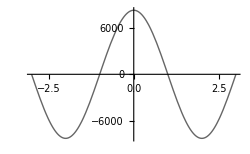

```mathematica
graphthreeFSine=Plot[fourierFSine[10,x],{x,-3,3},PlotStyle->GrayLevel[0.4]]
```

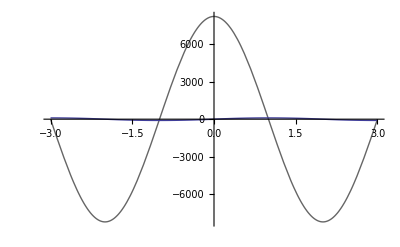

```mathematica
boththreeFSine=Show[graphthreeFSine,graphoneFSine]
```

```mathematica
graphsixFSine=Plot[fourierFSine[20,x],{x,-3,3},PlotStyle->GrayLevel[0.4]];
```

```mathematica
bothsixFSine=Show[graphsixFSine,graphoneFSine]
```

-Graphics-

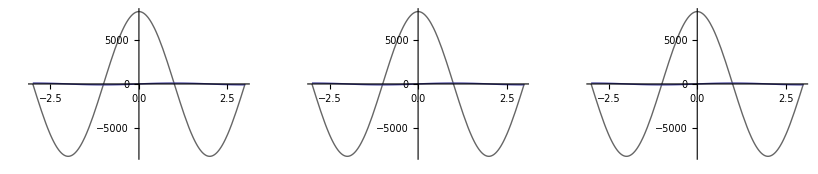

```mathematica
Show[GraphicsRow[{bothtwoFSine,boththreeFSine,bothsixFSine}]]
```

```mathematica
T[x_,y_,N_]:=(8*T0)/π^3∑_(k=1)^N 1/(2k+1)^3(Cosh[((2k+1)π y)/a]/Cosh[((2k+1)π b)/a])Sin[((2k+1)π x)/a]
```

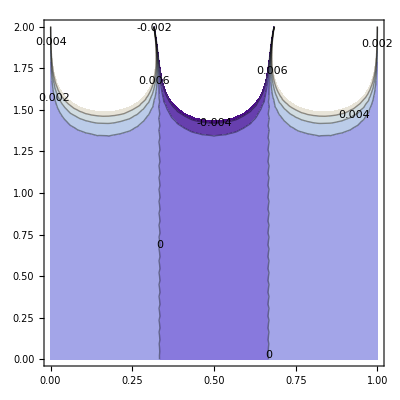

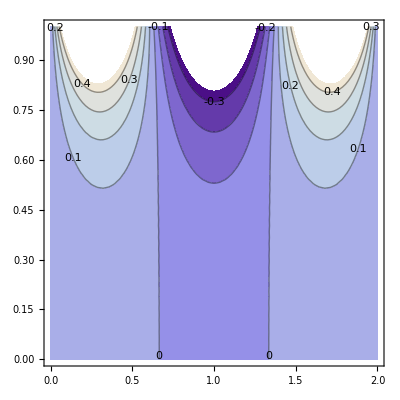
ProgressDialog[-Graphics-]

```mathematica
ContourPlot[T[x,y,5],{x,0,a},{y,0,b},ContourLabels->True]
```

```mathematica
(* Problem 2   *)
```

```mathematica
Clear[a,b,c,d,λ,F,Fn]
```

```mathematica
a=1;
b=2;
```

```mathematica
F[x_]:=(c*Cosh[(1+λ)^(1/2)*x]+d*Sinh[(1+λ)^(1/2)*x])
```

```mathematica
F[x]
```

c Cosh[x √(1+λ)]+d Sinh[x √(1+λ)]

```mathematica
D[F[x],x]
```

d √(1+λ) Cosh[x √(1+λ)]+c √(1+λ) Sinh[x √(1+λ)]

```mathematica
F'[0]
```

d √(1+λ)

```mathematica
Solve[{F'[0]==0,F[1]== 1},{c,d}]
```

{{c→Sech[√(1+λ)],d→0}}

```mathematica
c=Sech[√(1+λ[n])];
d=0;
```

```mathematica
λ[n_]:=(n^2 π^2)/b^2
```

```mathematica
Fn[x_,n_]=(c*Cosh[(1+λ[n])^(1/2)*x]+d*Sinh[(1+λ[n])^(1/2)*x])
```

Cosh[√(1+(n^2 π^2)/4) x] Sech[√(1+(n^2 π^2)/4)]

```mathematica
(* Still need to define the constant in front of the series *)
```

```mathematica
G[y_]:=e*Sin[(n π y)/b]+f*Cos[(n π y)/b]
```

```mathematica
Clear[e,f]
```

```mathematica
Solve[{G[0]==0,G[1]==1},{e,f}]
```

{{e→Csc[(n π)/2],f→0}}

```mathematica
e=Csc[(n π)/2];
f=0;
```

```mathematica
G[y]
```

Csc[(n π)/2] Sin[(n π y)/2]

```mathematica
Φ[x_,y_,N_]:=∑_(n=1)^N Fn[x,n]*G[y]
```

```mathematica
Φ[x,y,1]
```

Cosh[√(1+π^2/4) x] Sech[√(1+π^2/4)] Sin[(π y)/2]

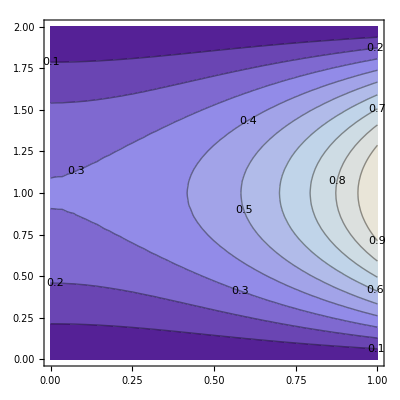

```mathematica
ContourPlot[Φ[x,y,1],{x,0,a},{y,0,b},ContourLabels->True]
```

```mathematica
(* Problem #3)
```

```mathematica
Clear[An,Bn,c,g,h]
```

```mathematica
L=1;
c=1;
g=1;
h=1;
```

```mathematica
y0[x_]:=g*Sin[(π x)/L];
v0[x_]:=h*Sin[(π x)/L];
```

```mathematica
y0[x]
```

Sin[π x]

```mathematica
v0[x]
```

Sin[π x]

```mathematica
w[n_]:=(n π c)/L
```

```mathematica
An[n_]:=Simplify[2/L∫_-L^L y0[x]*Sin[(n π x)/L]ⅆx,n∈Integers]
```

```mathematica
Bn[n_]:=2/(w[n]*L)Simplify[2/L∫_-L^L v0[x]*Sin[(n π x)/L]ⅆx,n∈Integers]
```

```mathematica
y[x_,t_,n_]:=(An[n]*Cos[w[n]*t]+Bn[n]*Sin[w[n]*t])Sin[(n π x)/L]
```

```mathematica
Plot[y[x,0,1],{x,0,L}]
```

Integrate::ilim: Invalid integration variable or limit(s) in {0.000020428571428571428`, -1, 1}.

NIntegrate::itraw: Raw object 0.0000204286 cannot be used as an iterator.

Integrate::ilim: Invalid integration variable or limit(s) in {0.02042859183673469`, -1, 1}.

General::stop: Further output of Integrate will be suppressed during this calculation.

NIntegrate::itraw: Raw object 0.0204286 cannot be used as an iterator.

General::stop: Further output of NIntegrate will be suppressed during this calculation.

-Graphics-

```mathematica
ContourPlot
```